## 4 hysterons

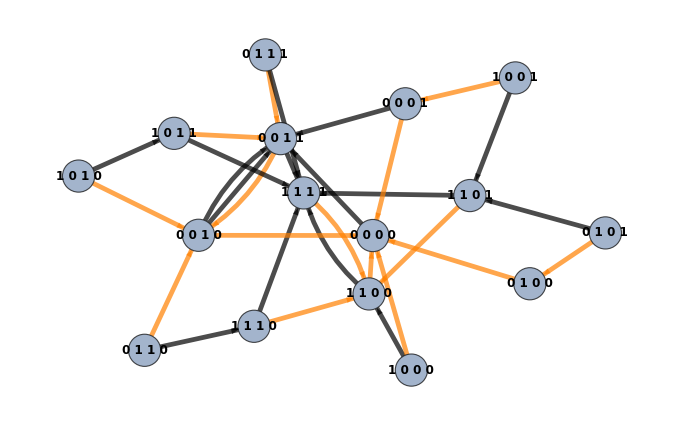

False

```mathematica
ClearAll@@Complement[Names["Global`*"],{"g2"}]


{a1,b1,c1,d1,a2,c2,a3,c3,a4,c4,k12,k13,k14,k23,k24,k34}={4,1,var,-1,4.1,-4,4.3,-3.9,3.9,-4.2,.5,0,0,-0.5,0,0.3};
var=-4.5;
equations={d1 g+c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2)-k13 (-x1+x3)-k14 (-x1+x4),d2 g-k21 (x1-x2)+c2 x2+b2 x2^2+a2 x2^3-k23 (-x2+x3)-k24 (-x2+x4),d3 g-k31 (x1-x3)-k32 (x2-x3)+c3 x3+b3 x3^2+a3 x3^3-k34 (-x3+x4),d4 g-k41 (x1-x4)-k42 (x2-x4)-k43 (x3-x4)+c4 x4+b4 x4^2+a4 x4^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=b1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2,x3,x4}}];

(*Set parameters here*)
bifurcationpts={x1,x2,x3,x4,g}/.NSolve[{equations==0,Det@jacobian==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x3]<3&&Abs[x4]<3},{x1,x2,x3,x4,g},Reals];
poseigenvalpts={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]],bifurcationpts[[n,4]],bifurcationpts[[n,5]]},Eigenvalues[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],x3->bifurcationpts[[n,3]],x4->bifurcationpts[[n,4]],g->bifurcationpts[[n,5]]}]],{n,1,Length@bifurcationpts}],#[[6]]>0&&#[[7]]>0&&#[[8]]>0&];
nullvectors=#[[7,4]]&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]],bifurcationpts[[n,4]],bifurcationpts[[n,5]]},Eigensystem[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],x3->bifurcationpts[[n,3]],x4->bifurcationpts[[n,4]],g->bifurcationpts[[n,5]]}]],{n,1,Length@bifurcationpts}],#[[6,1]]>0&&#[[6,2]]>0&&#[[6,3]]>0&];
maincondition=Table[(nullvectors[[n]].{D[D[equations[[1]],x1],x1]*nullvectors[[n,1]]^2,D[D[equations[[2]],x2],x2]*nullvectors[[n,2]]^2,D[D[equations[[3]],x3],x3]*nullvectors[[n,3]]^2,D[D[equations[[4]],x4],x4]*nullvectors[[n,4]]^2})/.{x1->poseigenvalpts[[n,1]],x2->poseigenvalpts[[n,2]],x3->poseigenvalpts[[n,3]],x4->poseigenvalpts[[n,4]]},{n,1,Length@nullvectors}];
states=Tally[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@Map[If[#>=0,1,0]&,poseigenvalpts,{2}]];
creationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]>0&];
annihilationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]<0&];
timedequations=equations/.{x1->x1[t],x2->x2[t],x3->x3[t],x4->x4[t]};
{x1'[t],x2'[t],x3'[t],x4'[t]}==timedequations;

eps=0.005;
eps2=-0.005;
maxN=Length[annihilationpoints];
maxN2=Length[creationpoints];

results1=Table[Module[{gval,sol,x1f,x2f,x3f,x4f},gval=annihilationpoints[[n,5]]+eps;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x3'[t]==(-timedequations[[3]]/. g->gval),x4'[t]==(-timedequations[[4]]/. g->gval),x1[0]==annihilationpoints[[n,1]],x2[0]==annihilationpoints[[n,2]],x3[0]==annihilationpoints[[n,3]],x4[0]==annihilationpoints[[n,4]]},{x1,x2,x3,x4},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]],x3[25]/. sol[[1]],x4[25]/. sol[[1]]}],{n,1,maxN}];
results2=Table[Module[{gval,sol,x1f,x2f,x3f,x4f},gval=creationpoints[[n,5]]+eps2;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x3'[t]==(-timedequations[[3]]/. g->gval),x4'[t]==(-timedequations[[4]]/. g->gval),x1[0]==creationpoints[[n,1]],x2[0]==creationpoints[[n,2]],x3[0]==creationpoints[[n,3]],x4[0]==creationpoints[[n,4]]},{x1,x2,x3,x4},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]],x3[25]/. sol[[1]],x4[25]/. sol[[1]]}],{n,1,maxN2}];

list1a={#[[1]],#[[2]],#[[3]],#[[4]]}&/@Map[If[#>=0,1,0]&,annihilationpoints,{2}];
list2a=Map[If[#>=0,1,0]&,results1,{2}];
list1b={#[[1]],#[[2]],#[[3]],#[[4]]}&/@Map[If[#>=0,1,0]&,creationpoints,{2}];
list2b=Map[If[#>=0,1,0]&,results2,{2}];
(*Convert 4-tuples to space-separated strings*)
toStr=StringJoin@Riffle[ToString/@#," "]&;
list1aStr=toStr/@list1a;
list2aStr=toStr/@list2a;
list1bStr=toStr/@list1b;
list2bStr=toStr/@list2b;
(*Arrowhead size*)
xx=0.04;
edges1=MapThread[Style[#1->#2,Black,Arrowheads[xx],Thickness[0.005]]&,{list1aStr,list2aStr}];
edges2=MapThread[Style[#1->#2,Orange,Arrowheads[xx],Thickness[0.005]]&,{list1bStr,list2bStr}];
(*Combine and draw the graph*)
g1=Graph[Join[edges1,edges2],VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Bold,12],VertexSize->0.55]

IsomorphicGraphQ[g1,g2]
```

```mathematica
Complement[EdgeList[g1],EdgeList[g2]]       (*Edges in g1 not g2*)
Complement[EdgeList[g2],EdgeList[g1]]       (*Edges in g2 not g1*)
Complement[VertexList[g1],VertexList[g2]]   (*In g1 but not g2*)
Complement[VertexList[g2],VertexList[g1]]   (*In g2 but not g1*)
```

{0 1 1 1->1 1 1 1}

{}

{}

{}

```mathematica
g2=g1;
```

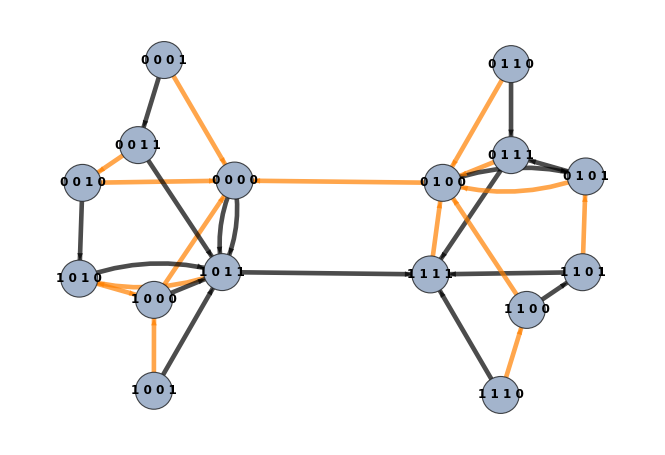

```mathematica
g2
```

## 2 hysterons

```mathematica
{-4.29936358873011,-4.299363588730108,-4.156977167021913,-4.156977167021911,-3.932147759286357,-3.9226281234561027,-3.879262544645338,-3.873868096093057,-3.8738680960930556,-3.597141497481379,-3.5516673269878827}
```

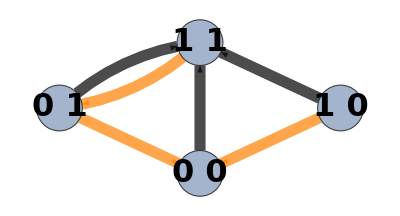

```mathematica
{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,0.2};var=-3.6;
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];bifurcationpts={x1,x2,g}/.NSolve[{equations==0,Det@jacobian==0&&Abs[x1]<3&&Abs[x2]<3},{x1,x2,g},Reals];
poseigenvalpts={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]]},Eigenvalues[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],g->bifurcationpts[[n,3]]}]],{n,1,Length@bifurcationpts}],#[[4]]>0&];
nullvectors=#[[5,2]]&/@Select[Table[Join[{bifurcationpts[[n,1]],bifurcationpts[[n,2]],bifurcationpts[[n,3]]},Eigensystem[jacobian/.{x1->bifurcationpts[[n,1]],x2->bifurcationpts[[n,2]],g->bifurcationpts[[n,3]]}]],{n,1,Length@bifurcationpts}],#[[4,1]]>0&];
maincondition=Table[(nullvectors[[n]].{D[D[equations[[1]],x1],x1]*nullvectors[[n,1]]^2,D[D[equations[[2]],x2],x2]*nullvectors[[n,2]]^2})/.{x1->poseigenvalpts[[n,1]],x2->poseigenvalpts[[n,2]]},{n,1,Length@nullvectors}];
states=Tally[{#[[1]],#[[2]]}&/@Map[If[#>=0,1,0]&,poseigenvalpts,{2}]];
creationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]<0&];
annihilationpoints=Select[MapThread[Append,{poseigenvalpts,maincondition}],#[[6]]>0&];
timedequations=equations/.{x1->x1[t],x2->x2[t]};
{x1'[t],x2'[t]}==timedequations;
eps=0.00068;
eps2=-0.00068;
maxN=Length[annihilationpoints];
maxN2=Length[creationpoints];
results1=Table[Module[{gval,sol,x1f,x2f},gval=annihilationpoints[[n,3]]+eps;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x1[0]==annihilationpoints[[n,1]],x2[0]==annihilationpoints[[n,2]]},{x1,x2},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]]}],{n,1,maxN}];
results2=Table[Module[{gval,sol,x1f,x2f},gval=creationpoints[[n,3]]+eps2;
sol=NDSolve[{x1'[t]==(-timedequations[[1]]/. g->gval),x2'[t]==(-timedequations[[2]]/. g->gval),x1[0]==creationpoints[[n,1]],x2[0]==creationpoints[[n,2]]},{x1,x2},{t,0,25}];
{x1[25]/. sol[[1]],x2[25]/. sol[[1]]}],{n,1,maxN2}];
list1a={#[[1]],#[[2]]}&/@Map[If[#>=0,1,0]&,annihilationpoints,{2}];list2a=Map[If[#>=0,1,0]&,results1,{2}];
list1b={#[[1]],#[[2]]}&/@Map[If[#>=0,1,0]&,creationpoints,{2}];list2b=Map[If[#>=0,1,0]&,results2,{2}];
toStr=StringJoin@Riffle[ToString/@#," "]&;
list1aStr=toStr/@list1a;list2aStr=toStr/@list2a;list1bStr=toStr/@list1b;list2bStr=toStr/@list2b;xx=0.14;
edges1=MapThread[Style[#1->#2,Black,Arrowheads[xx],Thickness[0.02]]&,{list1aStr,list2aStr}];
edges2=MapThread[Style[#1->#2,Orange,Arrowheads[xx],Thickness[0.02]]&,{list1bStr,list2bStr}];
(*Combine and draw the graph*)
g1=Graph[Join[edges1,edges2],VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Bold,32],VertexSize->0.35]
```

## Cusp points

```mathematica
Clear[var];{a1,b1,c1,d1,a2,c2,k12}={4,1.2,var,-1,4.3,-4,0.45};
equations={d1 g+2c1 x1+b1 x1^2+a1 x1^3-k12 (-x1+x2),d2 g-k21 (x1-x2)+2c2 x2+b2 x2^2+a2 x2^3};
k21=k12;k31=k13;k41=k14;k32=k23;k42=k24;k43=k34;b2=1;b3=b1;b4=b1;d2=d1;d3=d1;d4=d1;
jacobian=D[equations,{{x1,x2}}];
nullvector=(NullSpace[{{A11,A12},{A12,A12^2/A11}}])/.{A11->D[equations[[1]],x1],A12->D[equations[[1]],x2]};
cusppoints={x1,x2,g,var}/.NSolve[{equations==0&&Det@jacobian==0&&nullvector.{D[D[equations[[1]],x1],x1]*nullvector[[1,1]]^2,D[D[equations[[2]],x2],x2]*nullvector[[1,2]]^2}==0&&Abs[x1]<3&&Abs[x2]<3&&var<-1},{x1,x2,g,var},Reals];
eigenvalofcusp=#[[1]]&/@Table[Eigenvalues[jacobian/.{x1->cusppoints[[n,1]],x2->cusppoints[[n,2]],g->cusppoints[[n,3]],var->cusppoints[[n,4]]}],{n,1,Length@cusppoints}];
selectedcusps={#[[3]],#[[4]]}&/@Select[MapThread[Append,{cusppoints,eigenvalofcusp}],#[[5]]>0&];
crossingpoints={x1,x2,x11,x22,g,var}/.NSolve[{equations==0&&Det@jacobian==0&&(equations/.{x1->x11,x2->x22})==0&&(Det[jacobian/.{x1->x11,x2->x22}])==0&&Abs[x1]<3&&Abs[x2]<3&&Abs[x11]<3&&Abs[x22]<3&&var<-3.4},{x1,x2,x11,x22,g,var},Reals];
eigenvalofcrossing=({#[[1,1]],#[[2,1]]}&)/@Table[{Eigenvalues[jacobian/.{x1->crossingpoints[[n,1]],x2->crossingpoints[[n,2]],g->crossingpoints[[n,5]],var->crossingpoints[[n,6]]}],Eigenvalues[jacobian/.{x1->crossingpoints[[n,3]],x2->crossingpoints[[n,4]],g->crossingpoints[[n,5]],var->crossingpoints[[n,6]]}]},{n,1,Length@crossingpoints}];
selectedcrossings={#[[5]],#[[6]]}&/@Select[MapThread[Append,{crossingpoints,eigenvalofcrossing}],#[[7,1]]>0&&#[[7,2]]>0&];
ptstocheck=DeleteDuplicates[Chop@Sort@Join[selectedcrossings,selectedcusps]];
DeleteDuplicates[Chop[SortBy[Join[selectedcusps,selectedcrossings],#[[2]]&]]]
```

{{-3.76722,-4.79485},{5.02141,-4.45207},{-2.80148,-4.13526},{-2.80148,-4.13526},{4.08132,-3.93061},{4.08132,-3.93061}}